0.499176

0.449767

-0.490692

-0.494507

0.498535

0.349605

-0.499451

0.004532

0.499878

0.493683

-0.495941

-0.494263

0.498444

0.140815+0.219757 Cos[θ]-0.15476 (-1+3 Cos[θ]^2)-0.184538 (-3 Cos[θ]+5 Cos[θ]^3)+0.0527378 (3-30 Cos[θ]^2+35 Cos[θ]^4)+0.0408864 (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)-0.0317497 (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)+0.000309464 (-35 Cos[θ]+315 Cos[θ]^3-693 Cos[θ]^5+429 Cos[θ]^7)+0.00454228 (35-1260 Cos[θ]^2+6930 Cos[θ]^4-12012 Cos[θ]^6+6435 Cos[θ]^8)+0.00474253 (315 Cos[θ]-4620 Cos[θ]^3+18018 Cos[θ]^5-25740 Cos[θ]^7+12155 Cos[θ]^9)-0.00250435 (-63+3465 Cos[θ]^2-30030 Cos[θ]^4+90090 Cos[θ]^6-109395 Cos[θ]^8+46189 Cos[θ]^10)-0.00261202 (-693 Cos[θ]+15015 Cos[θ]^3-90090 Cos[θ]^5+218790 Cos[θ]^7-230945 Cos[θ]^9+88179 Cos[θ]^11)+0.000686565 (231-18018 Cos[θ]^2+225225 Cos[θ]^4-1021020 Cos[θ]^6+2078505 Cos[θ]^8-1939938 Cos[θ]^10+676039 Cos[θ]^12)

-Graphics3D-

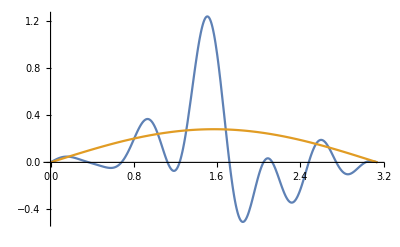

```mathematica
m1Y00=0.499176
m1Y01=0.449767
m1Y02=-0.490692
m1Y03=-0.494507
m1Y04=0.498535
m1Y05=0.349605
m1Y06=-0.499451
m1Y07=0.004532
m1Y08=0.499878
m1Y09=0.493683
m1Y010=-0.495941
m1Y011=-0.494263
m1Y012=0.498444

m1[x_]=m1Y00*SphericalHarmonicY[0,0,θ,0]+m1Y01*SphericalHarmonicY[1,0,θ,0]+m1Y02*SphericalHarmonicY[2,0,θ,0]+m1Y03*SphericalHarmonicY[3,0,θ,0]+m1Y04*SphericalHarmonicY[4,0,θ,0]+m1Y05*SphericalHarmonicY[5,0,θ,0]+m1Y06*SphericalHarmonicY[6,0,θ,0]+m1Y07*SphericalHarmonicY[7,0,θ,0]+m1Y08*SphericalHarmonicY[8,0,θ,0]+m1Y09*SphericalHarmonicY[9,0,θ,0]+
m1Y010*SphericalHarmonicY[10,0,θ,0]+m1Y011*SphericalHarmonicY[11,0,θ,0]+m1Y012*SphericalHarmonicY[12,0,θ,0]

SphericalPlot3D[{0.5651209027954321*m1[θ], 1/(2 √π)},{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
Plot[{m1[θ],1/(2 √π)},{θ,0,Pi}, PlotRange -> All]
```

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\90-15-300 with 40 species, Algorithim 1 and 2, 2D.jpg",%745,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\90-15-300 with 40 species, Algorithim 1 and 2, 2D.jpg

```mathematica
Show[%724,ViewPoint->{0,-∞,0}]
```

-Graphics3D-

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\90-15-300 with 40 species, Algorithim 1 and 2.jpg",%728,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\90-15-300 with 40 species, Algorithim 1 and 2.jpg

```mathematica
Show[%724,ViewPoint->Above]
```

-Graphics3D-

```mathematica
Export["D:\\Documents\\College\\OSU\\Research\\Sph. Harmonics proj\\SphHarEvol.1.cpp\\SphHarEvol.1.1\\90-15-300 with 40 species, Algorithim 1 and 2.jpg",%724,"JPEG"]
```

D:\Documents\College\OSU\Research\Sph. Harmonics proj\SphHarEvol.1.cpp\SphHarEvol.1.1\90-15-300 with 40 species, Algorithim 1 and 2.jpg

```mathematica
SphericalPlot3D[{ 1*SphericalHarmonicY[0,0,θ,0],SphericalHarmonicY[2,0,θ,0]  },{θ,0,Pi},{ϕ,0,Pi}, PlotRange -> All]
```

-Graphics3D-

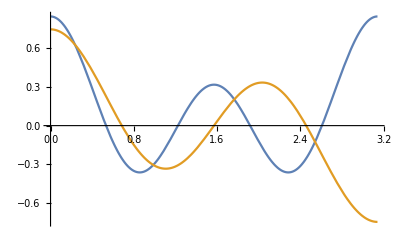

```mathematica
Plot[{ SphericalHarmonicY[4,0,θ,0],SphericalHarmonicY[3,0,θ,0] },{θ,0,Pi}, PlotRange -> All]
```

```mathematica
Integrate[Sin[θ](m1[x_]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

```mathematica
Integrate[Sin[θ](SphericalHarmonicY[0,0,θ,ϕ]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

```mathematica
1/(2 √π)
```

```mathematica
1/1.7695328469596348
```

0.565121

```mathematica
1/0.30019377340327935
```

3.33118

```mathematica
1/-0.04448930063925616
```

-22.4773

```mathematica
Integrate[Sin[θ](SphericalHarmonicY[0,0,θ,ϕ]*SphericalHarmonicY[5,0,θ,ϕ]), {θ,0,Pi},{ϕ,0,2 Pi}]
```

0

```mathematica
SphericalHarmonicY[0,0,θ,ϕ]^2
```

1/(4 π)

```mathematica
Simplify[(3/(4 π))^(1/3)]
```

(3/π)^(1/3)/2^(2/3)

```mathematica
N[2 √π]
```

3.54491